```mathematica
ntf[z_]:=1-z^-1;
FullSimplify[ComplexExpand[Abs[ntf[ⅇ^(ⅈ Ω)]]]]
```

√(2-2 Cos[Ω])

```mathematica
An[Ω_]:=√(2-2 Cos[Ω]);
ρn[Ω_]:=An[Ω]^2 σ^2/π;
TrigFactor[FullSimplify[ρn[Ω],Assumptions->Ω≥0&&Ω<π]]
∫_0^(π/R) ρn[Ω]ⅆΩ
```

(4 σ^2 Sin[Ω/2]^2)/π

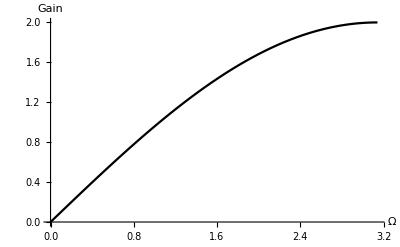

```mathematica
Plot[An[Ω],{Ω,0,π},PlotTheme->"Monochrome",AxesLabel->{Style["Ω",FontFamily->"Times",FontSize->12],Style["Gain",FontFamily->"Times",FontSize->12]}]
```

92.6097

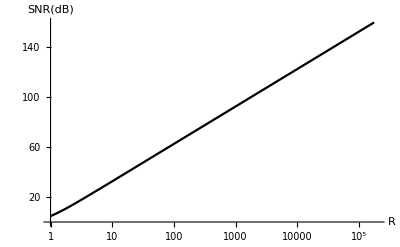

```mathematica
σ=√(1/12);
P[R_]:=(2 σ^2 (π-R Sin[π/R]))/(π R);
SNR[R_]:=10*Log10[0.5/P[R]];
N[SNR[1000]]
xticks={1,2,5,10,100,1000,10000,100000};
xgrids={1,2,5,10,20,50,100,200,500,1000,2000,5000,10000,20000,50000,100000,200000};
ygrids=Table[-20+10*k,{k,0,18}];
yticks={-20,0,20,40,60,80,100,120,140,160};
LogLinearPlot[SNR[R],{R,1,200000},PlotTheme->"Monochrome",GridLines->{xgrids,ygrids},Ticks->{xticks, yticks},PlotRange->{{1,200001},{0,160}},AxesLabel->{Style["R",FontFamily->"Times",FontSize->12],Style["SNR(dB)",FontFamily->"Times",FontSize->12]}]
```